```mathematica
Clear/@{verticesOfSimplex,configurationAdd,configurationMinus,partial,hasEmptyIntersection};

(*
The code is divided into 4 parts.
Part1: The input data of simplicial complex and excitation types. The variable: types describe how many kind of excitation you are considering, n is the order of excitation and dim is the dimension of moving operators. For example, if you want to consider a Z4 particle and a Z2 loop, then the data is "types=2; n={4,2}; dim={1,2};".
Part2: we process the input data of simplicial complex and excitation types, then generate the data of excitation model(A,S,∂,J).
	The size of A is dimH. 
	1. We describe an element in A using a integer in Range[dimH],and also provide addition and minus function configurationAdd[] and configurationMinus[].
	2. Moving operators correspond to integers in Range[operatorAmount]. partial[] maps s to ∂s. We provide functions actOperatorOn[s,a]=a+∂s and actInverseOperatorOn[s,a]=a-∂s.
3. A "process" means an element in the free group F(S). For example, s1^{-1}*s2*s3 is described by {{s1,-1},{s2,1},{s3,1}}. We provide functions processCommutator[], processHigherCommutator[],processRepeat[],processInverse[] to generate complicated processes.
	4. hasEmptyIntersection[] tells us whether a subset of operators is in J.
We want to mention that if you want to go beyond simplicial complex, you can construct these functions by yourself. If it is the case, then some variables and functions in the code is not important. cycles, configurations, operators and corresponding "index map" are functions to build a bijection between configurations, operators to their integer IDs. It is used in defining functions like addition and minus. If you already define addition and minus, then you will not need these variables anymore.
Some other functions like configurationGenerators and configurationName are not used in algorithm. They are only used to label the vertices in drawgraph[].
Part3: We use the data of excitation model to generate expression group E and Eid. The dimension dimE=dimH*operatorAmount. A useful function is theta[g,a], it returns the expression that acts the process g on a.
In our algorithm, we generated a minimum set of processes with empty support and apply them to all configurations. These expressions generate Eid. Finally it will do the SmithDecomposition and give the statistics.
Part4: Here we provide some functions used to analyze the explicit process of statistical phases. getExpression[i] returns the expression corresponds to the i-th entry of diag. After you get an expression, you can use drawgraph[] to draw it. Usually the result of getExpression[] is complicated, so you may want to try simplifyExpressionRamdomly[expression,trytimes] to simplify it.
You can also try your own process and use theta[g,a] to generate an expression. Then you can run orderOfExpression[expression]. If the result is 1, then your expression is a identity. If the result >1, then it is a statistical phase. If the result is 0, then it is not a statistical phase.
We also provide functions to study statistics as obstructions. You need to provide a list of processes {g1,...,gn} and run imposeIdentityProcess[{g1,...,gn}]. Then the program will impose theta[gi,a] as identities and do another SmithDecomposition. modifiedOrderOfExpression[] give the order of an expression in this new group. 
*)

(*Subscript[Z, n] excitation while moving operators are (dim)-simplex*)
types=1;
n={3,2,2};
dim={3,2,2};

(*Part1: data of complex*)
(*in a extended complex, there is a simplex of dimension=-1*)
simplex[-1]={1};
boundaryOfSimplex[simplexID_,0]:={1};

(*data of F-symbol(triangle)
simplex[0]={1,2,3};
simplex[1]={1,2,3};
boundaryOfSimplex[1,1]={1,2};
boundaryOfSimplex[2,1]={2,3};
boundaryOfSimplex[3,1]={1,3};*)


(*Data of tetrahedra in 2D: T-junction,...
simplex[0]={1,2,3,4};
simplex[1]={1,2,3,4,5,6};
simplex[2]={1,2,3,4};
boundaryOfSimplex[1,1]={1,2};
boundaryOfSimplex[2,1]={1,3};
boundaryOfSimplex[3,1]={1,4};
boundaryOfSimplex[4,1]={2,3};
boundaryOfSimplex[5,1]={2,4};
boundaryOfSimplex[6,1]={3,4};
boundaryOfSimplex[1,2]={1,2,4};
boundaryOfSimplex[2,2]={1,3,5};
boundaryOfSimplex[3,2]={2,3,6};
boundaryOfSimplex[4,2]={4,5,6};*)


(* centered tetrahedron, data of fermionic loops&membrane in 3D*)
(* Warning: labels and orders of these data cannot be changed!*)
simplex[0]={1,2,3,4,5};
simplex[1]={1,2,3,4,5,6,7,8,9,10};
simplex[2]={1,2,3,4,5,6,7,8,9,10};
simplex[3]={1,2,3,4,5};
boundaryOfSimplex[1,1]={1,2};
boundaryOfSimplex[2,1]={1,3};
boundaryOfSimplex[3,1]={1,4};
boundaryOfSimplex[4,1]={1,5};
boundaryOfSimplex[5,1]={2,3};
boundaryOfSimplex[6,1]={2,4};
boundaryOfSimplex[7,1]={2,5};
boundaryOfSimplex[8,1]={3,4};
boundaryOfSimplex[9,1]={3,5};
boundaryOfSimplex[10,1]={4,5};
boundaryOfSimplex[1,2]={1,2,5};
boundaryOfSimplex[2,2]={1,3,6};
boundaryOfSimplex[3,2]={1,4,7};
boundaryOfSimplex[4,2]={2,3,8};
boundaryOfSimplex[5,2]={2,4,9};
boundaryOfSimplex[6,2]={3,4,10};
boundaryOfSimplex[7,2]={5,6,8};
boundaryOfSimplex[8,2]={5,7,9};
boundaryOfSimplex[9,2]={6,7,10};
boundaryOfSimplex[10,2]={8,9,10};
boundaryOfSimplex[1,3]={1,2,4,7};
boundaryOfSimplex[2,3]={3,1,8,5};
boundaryOfSimplex[3,3]={2,3,6,9};
boundaryOfSimplex[4,3]={10,6,5,4};
boundaryOfSimplex[5,3]={7,8,9,10};



vectorDivision[a_,b_]:=LCM@@Table[If[#1==0&&#2!=0,0,If[#2==0,1,#1/GCD[#1,#2]]]&[a[[i]],b[[i]]],{i,Length[a]}];

(*Part2: Basic functions of simplicial complex*)
(*Here we define the homological boundary map. A i-chain c is discribed by the coefficient of every i-simplex*)
boundary[c_,dimension_]:=Module[{b=ConstantArray[0,Length[simplex[dimension-1]]],boundaries},
Do[
boundaries=boundaryOfSimplex[i,dimension];
Do[b[[boundaries[[j]]]]+=c[[i]]*(-1)^(j-1),{j,dimension+1}];
,{i,Length[simplex[dimension]]}];
Return[b];
];

(*return the array of all vertices of a simplex*)
verticesOfSimplex[simplexID_,dimension_]:=verticesOfSimplex[simplexID,dimension]=If[dimension<=0, {simplexID}, Union@@(verticesOfSimplex[#,dimension-1]&/@boundaryOfSimplex[simplexID,dimension])];
(*It is the same homological boundary map. But we use another discription of cochain: simply list some simplices.*)


(*part3: we construct the excitation model using the geometric data*)


cycles=ConstantArray[{},types];
cyclesIndexMap=ConstantArray[<||>,types];
cyclesGenerators=ConstantArray[{},types];
Do[
chains=Tuples[Range[0,n[[type]]-1],Length[simplex[dim[[type]]]]];
Do[If[!MemberQ[cycles[[type]],Mod[boundary[chain,dim[[type]]],n[[type]]]],AppendTo[cycles[[type]],Mod[boundary[chain,dim[[type]]],n[[type]]]];AppendTo[cyclesGenerators[[type]],chain];]
,{chain,chains}];
cyclesIndexMap[[type]]=AssociationThread[cycles[[type]]->Range[Length[cycles[[type]]]]];
,{type,types}]
configurations=Tuples[cycles];
configurationsIndexMap=AssociationThread[configurations->Range[Length[configurations]]];
configurationGenerators=Flatten/@Tuples[cyclesGenerators];
configurationName[generators_]:=Module[{terms,mathExpr},terms=Table[If[generators[[i]]==1,Subscript["U",i],If[generators[[i]]!=0,Superscript[Subscript["U",i],generators[[i]]],Nothing]],{i,Length[generators]}];
mathExpr=Row[terms,""];
Framed[mathExpr]];

dimH=Length[configurations];
configurationAdd[c1_,c2_]:=configurationAdd[c1,c2]=Module[{b3=ConstantArray[{},types],b1=configurations[[c1]],b2=configurations[[c2]]},
Do[b3[[type]]=Mod[b1[[type]]+b2[[type]],n[[type]]];
,{type,types}];
Return[configurationsIndexMap[b3]];
]
configurationMinus[c_]:=configurationMinus[c]=Module[{b3=ConstantArray[{},types],b=configurations[[c]]},
Do[b3[[type]]=Mod[-b[[type]],n[[type]]];
,{type,types}];
Return[configurationsIndexMap[b3]];
]
operatorList={};
Do[AppendTo[operatorList,{type,id}],{type,types},{id,Length[simplex[dim[[type]]]]}];
Print[" operatorList:",operatorList];
operatorsIndexMap=AssociationThread[operatorList->Range[Length[operatorList]]];
operatorAmount=Length[operatorList];

dimE=dimH*operatorAmount;
Print["The dimension of Hilbert space is ", dimH];
Print["The dimension of expression group is ", dimE];

partial[operators_]:=partial[operators]=Module[{op,b=Table[ConstantArray[0,Length[simplex[dim[[type]]-1]]],{type,types}],boundaries},
Do[op=operatorList[[Abs[id]]];
boundaries=boundaryOfSimplex[op[[2]],dim[[op[[1]]]]];
Do[b[[op[[1]]]][[boundaries[[j]]]]+=(-1)^(j-1)*Sign[id],{j,dim[[op[[1]]]]+1}];
,{id,operators}];
Do[b[[type]]=Mod[b[[type]],n[[type]]];
,{type,types}];
Return[configurationsIndexMap[b]];
];
actOperatorOn[operatorIndex_,configurationIndex_]:=      configurationAdd[configurationIndex,partial[{operatorIndex}] ]   ;


(*return g^{-1}*)
processInverse[g_]:=Reverse[-#&/@g];

processRepeat[g_,k_]:=Join@@Table[g,k];
(* return [g1,g2]=g2^{-1}g1^{-1}g2g1 *)
processCommutator[g1_,g2_]:= Join[processInverse[Join[g2,g1]],Join[g1,g2]];
(*input:{g1,g2,...gn} return:[[g1,g2],...,gn]*)
processHigherCommutator[operators_]:=Fold[processCommutator[#2,#1]&,Reverse[operators]];
theta[operators_,beginning_]:=Module[{configuration,expression},
configuration=beginning;
expression=ConstantArray[0,{Length[operatorList],Length[configurations]}];
Do[If[operator>0,expression[[operator,configuration]]++; configuration=actOperatorOn[operator,configuration];,
configuration=actOperatorOn[operator,configuration];expression[[Abs[operator],configuration]]--;]

,{operator,Reverse[operators]}];
Return[Flatten[expression]];
]
applyProcessOn[operators_,beginning_]:=configurationAdd[beginning,partial[operators]];


support[operatorID_]:=verticesOfSimplex[operatorList[[operatorID]][[2]],dim[[operatorList[[operatorID]][[1]]]]];
hasEmptyIntersection[operators_]:=hasEmptyIntersection[operators]=(Intersection@@(support/@operators)=={});



(*Part4: Now we generate commutators that generated the identity subgroup of E*)
isReducedCommutator[fixedOperators_,hArray_]:=Module[{i},
(*If the intersection is not empty, the it is not a identity*)
If[!hasEmptyIntersection[Union[hArray,fixedOperators]],Return[False]];
(* Try throw away some element in hArray. If we cannot do it, then it is reduced*)

For[i=1,i<=Length[hArray],i++,If[hasEmptyIntersection[Union[Delete[hArray,i],fixedOperators]],Return[False]]];
Return[True];
];

commutators={};

Block[{hArraysList},
hArraysList=Subsets[Range[operatorAmount],5];
Do[

If[Length[hArray]<=1,Continue[]];
Do[
If[isReducedCommutator[{hArray[[1]],hArray[[j]]},Delete[hArray,{{1},{j}}]],AppendTo[commutators,processHigherCommutator[{#}&/@Join[Delete[hArray,{{1},{j}}],{hArray[[1]],hArray[[j]]}]]];];
,{j,2,Length[hArray]}]

,{hArray,hArraysList}]

]

(*Print[Length[commutators]," commutators: ",commutators];*)



(*Part5: Now we generete all identities. Every generator of identities is an expression. An expression is a two dimension array, labeled by operator and configuration, which correspond to configurations and moving operators applied on it.*)
identities={};
identitiesCount=0;
Print["Time used: ",AbsoluteTiming[
Block[{g1,g2,hArray,isConfigurationUsed,identity,vars,sign,beginningConfiguration,x},

Do[

Do[
x=theta[commutator,configuration];
If[MemberQ[identities,x]||MemberQ[identities,-x],Continue[];];
AppendTo[identities,x];
identitiesCount++;
,{configuration,dimH}];
(*compress identities, avoiding it becomin too large *)  
If[Length[identities]>2*dimE,Print["compression!"];
Module[{u,r},
{u,r}=HermiteDecomposition[identities];
identities=Select[r,Plus@@Abs/@#!=0&];
];
];

,{commutator,commutators}];
];

Print[identitiesCount," identities are generated."];

{U,R,V}=SmithDecomposition[Transpose[identities]];
diag=PadRight[Diagonal[R],dimE];
Print[diag];
Print["Nontrivial diagonal elements:", Select[AssociationThread[Range[Length[diag]]->diag],#>1&]];

][[1]]," seconds."];


(*
Some useful functions to analyze the concrete expression*)
inverseU=Inverse[U];
getExpression[index_]:=inverseU[[All,index]];
(*orderOfExpression[e_]:=Reverse[diag][[FirstPosition[Reverse[U.e],_?(#!=0&),{Length[diag]}]]]*)
orderOfExpression[e_]:=vectorDivision[diag,U.e];
identityProcessPool={};
Block[{hArraysList},Do[
hArraysList=Subsets[Range[operatorAmount],5];
Do[
If[isReducedCommutator[{i,j},hArray],AppendTo[identityProcessPool,processHigherCommutator[{{#,1}}&/@Join[{i,j},hArray]]];];

,{hArray,hArraysList}]
,{i,1,operatorAmount-1},{j,i+1,operatorAmount}]
];

simplifyExpressionRandomly[expression_,tryTimes_]:=Block[{temp,c},
exp=expression;
(*Print["size: ",Dynamic[Plus@@Abs[exp]]];*);
Do[
temp=exp+RandomChoice[{1,-1}]*theta[RandomChoice[identityProcessPool],RandomInteger[{1,dimH}]];
If [Plus@@Abs[temp]<=Plus@@Abs[exp],exp=temp;];
,tryTimes];
Return[exp];
]
drawGraph[expression_]:=Module[{nodes,edges,expressionMatrix},
nodes={};
edges={};
expressionMatrix=Partition[expression,dimH];
Do[
If[expressionMatrix[[op,configuration]]!=0,AppendTo[edges,Labeled[Style[DirectedEdge[configuration,actOperatorOn[Abs[op],configuration]],If[expressionMatrix[[op,configuration]]>0,Red,Blue]],Style[Subscript[(ToString[expressionMatrix[[op,configuration]]]<>"×U"), op],FontSize->20]]
];nodes=Union[nodes,{configuration,actOperatorOn[op,configuration]}];];
 
,{op,Range[Length[operatorList]]},{configuration,Range[dimH]}];
Graph[edges,VertexLabels->Table[v->configurationName[configurationGenerators[[v]]],{v,nodes}]]
]

modifiedU=U;
modifiedR=R;
modifiedDiag=diag;
modifiedIdentities=identities;
imposeIdentityProcess[processes_]:=Module[{},
modifiedIdentities=identities;
Do[
Do[AppendTo[modifiedIdentities,theta[process,configuration]];,{configuration,dimH}];
If[Length[modifiedIdentities]>2*dimE,Print["compression!"];
Module[{u,r},
{u,r}=HermiteDecomposition[modifiedIdentities];
modifiedIdentities=Select[r,Plus@@Abs/@#!=0&];
];
];
,{process,processes}];

{modifiedU,modifiedR,modifiedV}=SmithDecomposition[Transpose[modifiedIdentities]];
modifiedDiag=PadRight[Diagonal[modifiedR],dimE];
]
modifiedOrderOfExpression[e_]:=vectorDivision[modifiedDiag,modifiedU.e];
```

operatorList:{{1,1},{1,2},{1,3},{1,4},{1,5}}

The dimension of Hilbert space is 81

The dimension of expression group is 405

324 identities are generated.

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

Nontrivial diagonal elements:<|70→3|>

Time used: 0.940177 seconds.

```mathematica
theta[processCommutator[{3},{2,2,2}],1]//drawGraph
```

-Graphics-

Set::write: Inherited[State] 中的标签 Inherited 被保护.

```mathematica
theta[processCommutator[{3},{2,2,2}],1]//orderOfExpression
```

3

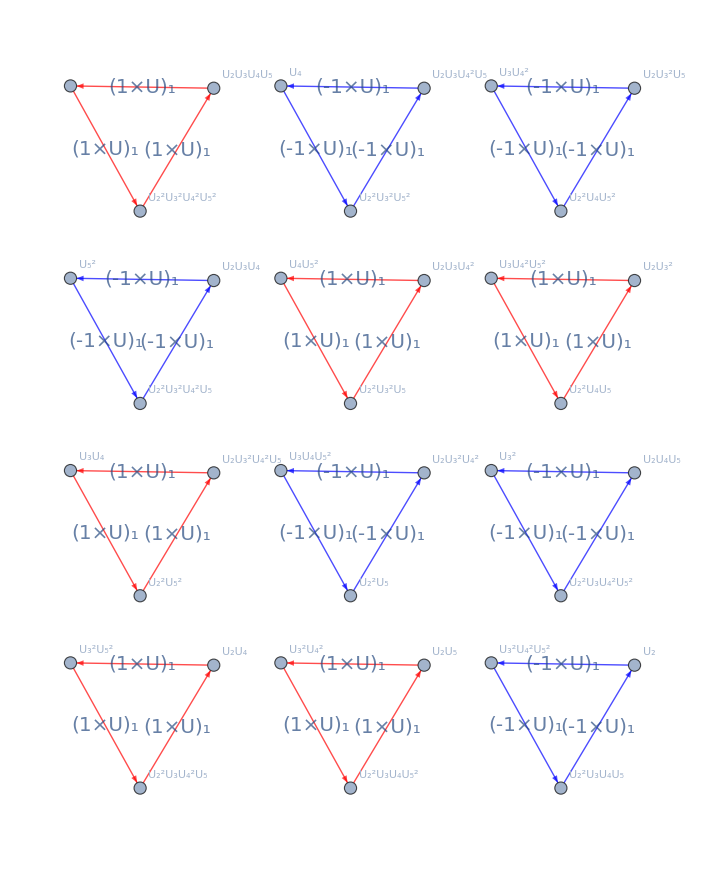

```mathematica
c=processCommutator[{2},processRepeat[{1},3]];
p=Join[processInverse[processRepeat[{3,4},3]],processRepeat[Join[{3},processInverse[c],{4},c],3]];
theta[p,1]//drawGraph
```

```mathematica
p
```

{-4,-3,-4,-3,-4,-3,3,-5,-5,-5,-2,5,5,5,2,4,-2,-5,-5,-5,2,5,5,5,3,-5,-5,-5,-2,5,5,5,2,4,-2,-5,-5,-5,2,5,5,5,3,-5,-5,-5,-2,5,5,5,2,4,-2,-5,-5,-5,2,5,5,5}